# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 03

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

NOTE: This question was inadvertently included in both Assignments 02 and 03.

Use FinancialBond[ ] to compute the following:

A newly issued $10,000 bond with a ten-year term has a 4% coupon rate and pays semi-annually. The current market yield for a ten-year bond of this type is 3.7%. What is the current market price of the bond?

A $10,000 bond with a five-year term, a 3.7% coupon rate paying semi-annually was issued eight months ago. The current market yield is 3.5%.

What is the current price of the bond?

What is the accrued interest on the bond?

Consider a $10,000 semi-annual bond with a twenty-year term and a 4.5% coupon rate. The bond was issued five-years ago and currently trades at a price of $10,500. What is the yield on the bond?

### Solution

A newly issued $10,000 bond with a ten-year term has a 4% coupon rate and pays semi-annually. The current market yield for a ten-year bond of this type is 3.7%. What is the current market price of the bond?

```mathematica
FinancialBond[{"Coupon"->0.04,"FaceValue"->10000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.037,"Settlement"->0}]
```

10248.9

A $10,000 bond with a five-year term, a 3.7% coupon rate paying semi-annually was issued eight months ago. The current market yield is 3.5%.

What is the current price of the bond?

What is the accrued interest on the bond?

```mathematica
FinancialBond[{"Coupon"->0.037,"FaceValue"->10000,"Maturity"->5,"CouponInterval"->1/2},{"InterestRate"->0.035,"Settlement"->8/12},{"Value","AccruedInterest"}]
```

{10079.4,61.6667}

Consider a $10,000 semi-annual bond with a twenty-year term and a 4.5% coupon rate. The bond was issued five-years ago and currently trades at a price of $10,500. What is the yield on the bond?

```mathematica
FindRoot[10500.==FinancialBond[{"Coupon"->0.045,"FaceValue"->10000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->y,"Settlement"->5}],{y,0.045}]
```

{y→0.0340402}

## Question 2

Consider two assets with mean returns, standard deviations and correlation matrix:

μ=(0.08
0.05)

σ=(0.10
0.04)

C=(1 | 0.4
0.4 | 1)

ℳ_1=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1}

Compute the covariance matrix Σ.

Consider the following portfolio optimization problem ℳ_1 (short positions allowed):

ℳ_1=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1}

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

If the risk-free rate r_f=0.01, what is the tangent portfolio?

Consider the following portfolio optimization problem ℳ_2 (no short positions allowed):

ℳ_2=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1∧x_i≥0}

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

Compare the efficient frontiers of ℳ_1 and ℳ_2.

### Solution

```mathematica
vnMu={0.08,0.05};
vnSigma={0.1,0.04};
mnCor={{1.,0.4},{0.4,1.}};
```

Compute the covariance matrix Σ.

```mathematica
mnCovar=KroneckerProduct[vnSigma,vnSigma]mnCor;
```

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

ℳ_1=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1}

x=λ Σ^-1 μ+((1-λ 1^T Σ^-1 μ)/(1^T Σ^-1 1)) Σ^-1 1

```mathematica
xEffPort[λ_,μ_,Σ_]:=Block[
{mnInvΣ,vnOne},
mnInvΣ=Inverse[Σ];
vnOne=Array[1.&,Length[μ]];
λ mnInvΣ.μ+((1-λ vnOne.mnInvΣ.μ)/(vnOne.mnInvΣ.vnOne))mnInvΣ.vnOne
];
```

```mathematica
mnEffPorts=Table[xEffPort[λ,vnMu,mnCovar],{λ,0,0.35,0.025}]
```

{{2.27374×10^-17,1.},{0.0892857,0.910714},{0.178571,0.821429},{0.267857,0.732143},{0.357143,0.642857},{0.446429,0.553571},{0.535714,0.464286},{0.625,0.375},{0.714286,0.285714},{0.803571,0.196429},{0.892857,0.107143},{0.982143,0.0178571},{1.07143,-0.0714286},{1.16071,-0.160714},{1.25,-0.25}}

```mathematica
mnEffFront={√(#.mnCovar.#),vnMu.#}&/@mnEffPorts
```

{{0.04,0.05},{0.0408285,0.0526786},{0.0432187,0.0553571},{0.0469327,0.0580357},{0.0516859,0.0607143},{0.0572198,0.0633929},{0.0633302,0.0660714},{0.0698659,0.06875},{0.0767184,0.0714286},{0.0838099,0.0741071},{0.0910847,0.0767857},{0.0985022,0.0794643},{0.106032,0.0821429},{0.113653,0.0848214},{0.121347,0.0875}}

Compute and plot a mean-variance efficient frontier for a portfolio consisting of these two assets.

ℳ_2=min_x {1/2 x^T Σ x-λ μ^T x |  1^T x=1∧x_i≥0}

```mathematica
x={x1,x2};
```

```mathematica
xEffPortNoShorts[λ_,vnMean_,mnCov_]:=x/.Last[NMinimize[{(x.mnCov.x)/2-λ vnMean.x,And@@Join[{Total[x]==1},#≥0&/@x]},x]];
```

```mathematica
mnEffPortNoShort=Table[
xEffPortNoShorts[λ,vnMu,mnCovar],
{λ,0.0,0.35,0.025}
]
```

{{1.47094×10^-8,1.},{0.0892858,0.910714},{0.178571,0.821429},{0.267857,0.732143},{0.357143,0.642857},{0.446429,0.553571},{0.535714,0.464286},{0.625,0.375},{0.714286,0.285714},{0.803571,0.196429},{0.892857,0.107143},{0.982143,0.0178572},{1.,0.},{1.,0.},{1.,0.}}

```mathematica
mnEffFrontNoShort={√(#.mnCovar.#),vnMu.#}&/@mnEffPortNoShort
```

{{0.04,0.05},{0.0408285,0.0526786},{0.0432187,0.0553571},{0.0469327,0.0580357},{0.0516859,0.0607143},{0.0572198,0.0633929},{0.0633302,0.0660714},{0.0698659,0.06875},{0.0767184,0.0714286},{0.0838099,0.0741071},{0.0910847,0.0767857},{0.0985022,0.0794643},{0.1,0.08},{0.1,0.08},{0.1,0.08}}

Compare the efficient frontiers of ℳ_1 and ℳ_2.

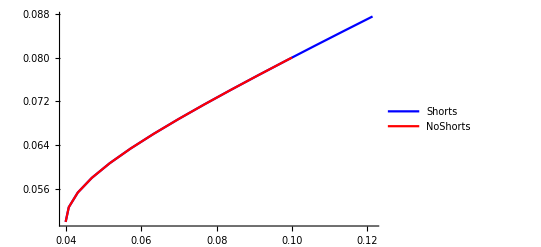

```mathematica
ListLinePlot[{mnEffFront,mnEffFrontNoShort},PlotStyle->{Blue,Red},PlotLegends->{"Shorts","NoShorts"}]
```

## Question 3

Use FinancialData[ ] to download the data required to complete the following:

Secure the closing price data for Microsoft and Apple to 2019-06-30.

Plot the closing price of Microsoft and Apple on the same graph.

Compute the daily returns for Microsoft and Apple and plot them on separate graphs.

Generate a table which contains for each stock in the Dow Jones Industrial index: the ticker symbol, name, and market capitalization.

### Solution

```mathematica
mnMSFT=FinancialData["MSFT",{{2018,1,1},{2018,9,29}},Method->"Legacy"];
mnAAPL=FinancialData["AAPL",{{2018,1,1},{2018,9,29}},Method->"Legacy"];
```

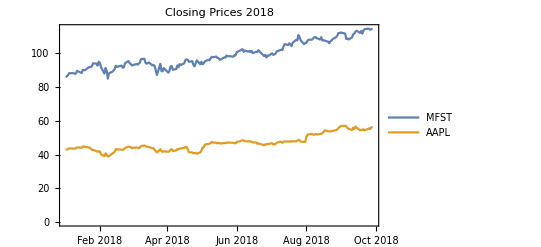

```mathematica
DateListPlot[{mnMSFT,mnAAPL},PlotLegends->{"MFST","AAPL"},PlotLabel->"Closing Prices 2018"]
```

```mathematica
mnMSFTRet=Transpose@{Rest[mnMSFT⟦All,1⟧],(Rest[#]-Most[#])/Most[#]&[mnMSFT⟦All,2⟧]};
mnAAPLRet=Transpose@{Rest[mnAAPL⟦All,1⟧],(Rest[#]-Most[#])/Most[#]&[mnAAPL⟦All,2⟧]};
```

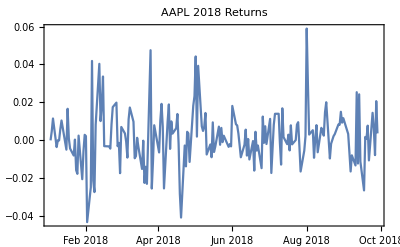

```mathematica
DateListPlot[mnAAPLRet,PlotRange->All,PlotLabel->"AAPL 2018 Returns"]
```

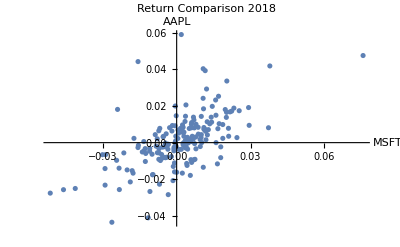

```mathematica
ListPlot[{mnMSFTRet⟦All,2⟧,mnAAPLRet⟦All,2⟧}ᵀ,AxesLabel->{"MSFT","AAPL"},PlotLabel->"Return Comparison 2018",PlotRange->All]
```

```mathematica
vsDJITickers=FinancialData["^DJI","Members"]
```

{NYSE:MMM,NYSE:AXP,NASDAQ:AAPL,NYSE:BA,NYSE:CAT,NYSE:CVX,NASDAQ:CSCO,NYSE:KO,NYSE:DIS,NYSE:DOW,NYSE:XOM,NYSE:GS,NYSE:HD,NASDAQ:INTC,NYSE:IBM,NYSE:JNJ,NYSE:JPM,NYSE:MCD,NYSE:MRK,NASDAQ:MSFT,NYSE:NKE,NYSE:PFE,NYSE:PG,NYSE:RTX,NYSE:TRV,NYSE:UNH,NYSE:VZ,NYSE:V,NASDAQ:WBA,NYSE:WMT}

```mathematica
vnDJIMktCap=FinancialData[#,"MarketCap"]&/@vsDJITickers
```

{9.76641×10^10 $,8.32859×10^10 $,1.82723×10^12 $,9.09553×10^10 $,8.25202×10^10 $,1.46041×10^11 $,1.68533×10^11 $,2.16705×10^11 $,2.32443×10^11 $,3.73303×10^10 $,1.57248×10^11 $,6.70467×10^10 $,2.9623×10^11 $,2.12182×10^11 $,1.09327×10^11 $,3.92765×10^11 $,2.99732×10^11 $,1.63903×10^11 $,2.17034×10^11 $,1.51648×10^12 $,1.78857×10^11 $,2.03549×10^11 $,3.41999×10^11 $,9.52493×10^10 $,2.82587×10^10 $,2.92722×10^11 $,2.49732×10^11 $,4.31127×10^11 $,3.20011×10^10 $,3.83378×10^11 $}

```mathematica
vsDJINames=FinancialData[#,"Name"]&/@vsDJITickers
```

{3M,American Express,Apple,Boeing,Caterpillar,Chevron,Cisco,Coca-Cola,Disney,Dow,Exxon Mobil,Goldman Sachs,Home Depot,Intel,IBM,Johnson & Johnson,JPMorgan Chase,McDonald's,Merck & Co.,Microsoft,Nike,Pfizer,Procter & Gamble,Raytheon Technologies Corp,Travelers,UnitedHealth,Verizon Communications,Visa,Walgreens Boots Alliance Inc,Wal-Mart Stores}

```mathematica
TableForm[{vsDJITickers,vsDJINames,vnDJIMktCap}ᵀ,TableHeadings->{Automatic,{"Symbol","Name","Mkt Cap"}}]
```

| Symbol | Name | Mkt Cap
1 | NYSE:MMM | 3M | 9.76641×10^10 $
2 | NYSE:AXP | American Express | 8.32859×10^10 $
3 | NASDAQ:AAPL | Apple | 1.82723×10^12 $
4 | NYSE:BA | Boeing | 9.09553×10^10 $
5 | NYSE:CAT | Caterpillar | 8.25202×10^10 $
6 | NYSE:CVX | Chevron | 1.46041×10^11 $
7 | NASDAQ:CSCO | Cisco | 1.68533×10^11 $
8 | NYSE:KO | Coca-Cola | 2.16705×10^11 $
9 | NYSE:DIS | Disney | 2.32443×10^11 $
10 | NYSE:DOW | Dow | 3.73303×10^10 $
11 | NYSE:XOM | Exxon Mobil | 1.57248×10^11 $
12 | NYSE:GS | Goldman Sachs | 6.70467×10^10 $
13 | NYSE:HD | Home Depot | 2.9623×10^11 $
14 | NASDAQ:INTC | Intel | 2.12182×10^11 $
15 | NYSE:IBM | IBM | 1.09327×10^11 $
16 | NYSE:JNJ | Johnson & Johnson | 3.92765×10^11 $
17 | NYSE:JPM | JPMorgan Chase | 2.99732×10^11 $
18 | NYSE:MCD | McDonald's | 1.63903×10^11 $
19 | NYSE:MRK | Merck & Co. | 2.17034×10^11 $
20 | NASDAQ:MSFT | Microsoft | 1.51648×10^12 $
21 | NYSE:NKE | Nike | 1.78857×10^11 $
22 | NYSE:PFE | Pfizer | 2.03549×10^11 $
23 | NYSE:PG | Procter & Gamble | 3.41999×10^11 $
24 | NYSE:RTX | Raytheon Technologies Corp | 9.52493×10^10 $
25 | NYSE:TRV | Travelers | 2.82587×10^10 $
26 | NYSE:UNH | UnitedHealth | 2.92722×10^11 $
27 | NYSE:VZ | Verizon Communications | 2.49732×10^11 $
28 | NYSE:V | Visa | 4.31127×10^11 $
29 | NASDAQ:WBA | Walgreens Boots Alliance Inc | 3.20011×10^10 $
30 | NYSE:WMT | Wal-Mart Stores | 3.83378×10^11 $

## Question 4

Recently, yields on the sovereign debt of several European countries have turned negative. In effect, bond holders are paying these governments for holding their capital.

Yields on German Bunds can be found at

	https://www.bloomberg.com/markets/rates-bonds/government-bonds/germany. 

Recent data for late September 2019 were {term, yield}:

```mathematica
mnBundYields={{2,-0.0076},{5,-0.007},{10,-0.0059},{30,-0.0012}};
```

A reasonable estimate for the yield curve can be found using a second-order spline interpolation.

Consider an older Bund with a 10-year term, semi-annual payments, a face amount of €10,000 and a coupon rate of 0.002%. The bond is 3 years into its term. What is the current market price of the bond?

### Solution

```mathematica
xBundYield=Interpolation[mnBundYields,Method->"Spline",InterpolationOrder->2];
```

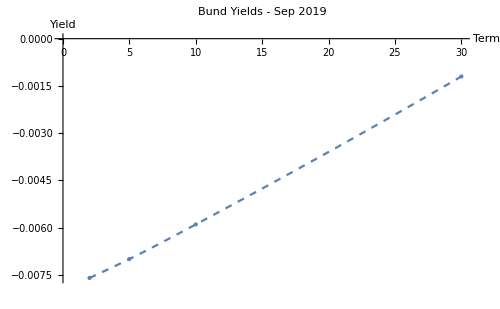

```mathematica
Show[
ListPlot[mnBundYields,PlotStyle->{PointSize[Large]}],
Plot[xBundYield[t],{t,2,30},PlotStyle->{Dashed}],
PlotLabel->"Bund Yields - Sep 2019",
AxesLabel->{"Term","Yield"},
ImageSize->500
]
```

The bond can be viewed as a 7-year bond:

```mathematica
nBundYield7=xBundYield[7]
```

-0.00657126

```mathematica
FinancialBond[{"FaceValue"->10000,"Coupon"->0.002,"Maturity"->7,"CouponInterval"->1/2},{"InterestRate"->nBundYield7,"Settlement"->0}]
```

10615.

Alternately, we could use TimeValue[ ]:

```mathematica
nCoupon=(10000 0.002)/2
```

10.

```mathematica
TimeValue[Annuity[{nCoupon,{0,10000}},7,1/2],EffectiveInterest[nBundYield7,1/2],0]
```

10615.

The bond can equivalently by viewed as a 10-year bond 3 years into its term (with, of course, the appropriate 7-year yield):

```mathematica
FinancialBond[{"FaceValue"->10000,"Coupon"->0.002,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->nBundYield7,"Settlement"->3}]
```

10615.